4.01+x ((8.01+2.77556×10^-17 ⅈ)+x (5.+x))

c^2+(2 a+b-3 x) (b-x)

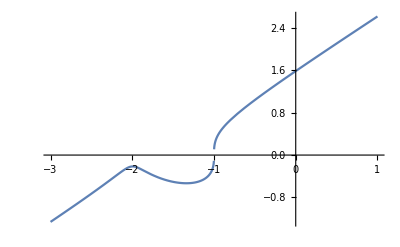

```mathematica
aa=-1;
bb=-2;
cc=0.1;

FullSimplify[Expand[(x-aa)*(x-(bb+I*cc))*(x-(bb-I*cc))]]

ff[x_,a_,b_,c_]:=-(c^2+(b-x)^2) (a-x)
dd[x_,a_,b_,c_]:=c^2+(2 a+b-3 x) (b-x)

FullSimplify[D[ff[x,a,b,c],x]]

Plot[Sign[ff[x,aa,bb,cc]]*Abs[ff[x]]^(1/3),{x,-3,1}]
Plot[Sign[dd[x,aa,bb,cc]]*Abs[ff[x]]^(1/2),{x,-3,1}]
```